## Subradiance-protected excitation spreading for collimated photon emission

P. Huft
See paper by K. Ballantine, J. Ruostekoski

## personal notes

### Questions

Why can a system which is excited with a single photon be adequately described by classical E&M?

The collective mode which is predominantly coupled by the initial excitation (after rotating the polarization to be normal to the atom grid plane) decays slowly, i.e. is subradiant, while other modes decay superradiantly. Why do these other modes see an a higher rate of decay than independent decay? Does it just “come out of the math” as with the √N enhancement of ensemble Rabi flopping?

## setup

System description: atomnum two-level atoms arranged in a 2D square grid with equal periodicity in x and y. The lower level is has only one angular momentum state (J=0) while the upper state has three Zeeman sublevels (J=1).

```mathematica
(*PHYSICAL CONSTANTS*)
(*ℏ = 6.62607015*^-34/(2π);*)
μ0 =4π*10^-7;
c = 299792458;
ϵ0 = 1/(c^2 μ0);
ee = 1.602*^-19; (*electron charge*)
a0 = 5.27*^-11; (*Bohr radius*)
(*PARAMETERS and other DEFINITIONS*)
atomnum = 9*9; (*should be an odd perfect square*)
J = 1; (*upper level total angular
 momentum*) 
λ = 7.8*10^-7;
k=2π/λ;
matelem = ee a0; (*just assume a general matrix element is of this order for now.*)
γ = matelem^2 k^3/(6 π ϵ0); (*single two-level atom linewidth, ℏ=1*)
pol = Range[3];(*pol[[μ]]/.u->1,2,3 for polarization σ=-1,0,+1 *)
Subscript[Δ, μ_]:= {0,0,0}[[μ]]; (*no Zeeman splitting for now*)
deg = 2J+1;
dim = deg*atomnum;(*Hamiltonian shape is dim x dim, with state vector = dim*)

(*FUNCTIONS*)
idx[i_,j_,n_]:=(i-1)n+j//Simplify; (*get 1D atom idx from 2D coordinate indices*)
Subscript[r, i_,j_]:={0,Mod[j-1,n]-Mod[i-1,n],Floor[(j-1)/n]-Floor[(i-1)/n]}/.n->√atomnum;(*vector between atoms i,j in units lattice spacing*)
unit[v_]:=v/(√(v.v));
(*sphrWave[x_,y_,z_]:=(ⅇ^(ⅈ k √(x^2+y^2+z^2)))/(4 π √(x^2+y^2+z^2));(*spherical wave*)
Subscript[Kδ, μ_,ν_]:=KroneckerDelta[SymbolName[μ],SymbolName[ν]];(*symbolic Kronecker delta*)
dipOp[α_,β_]=(D[#,α]D[#,β]-Subscript[Kδ, α,β] Laplacian[#,{x,y,z}])&; (*derivative op in the expression for positive freq. component of Green tensor element*)
Subscript[G, α_,β_]:=dipOp[α,β][sphrWave[x,y,z]]-Subscript[Kδ, α,β] DiracDelta[√(x^2+y^2+z^2)];
(*element (α,β) of dipole radiation Green function tensor in free space*)
GTensor = Table[Subscript[G, α,β]+(Subscript[Kδ, α,β] DiracDelta[√(x^2+y^2+z^2)])/3,{α,{x,y,z}},{β,{x,y,z}}];(*G' in paper*)*)
GdotP[r_,p_]:=ⅇ^(ⅈ k √(r.r))/(4 π √(r.r))(Cross[Cross[unit[r],p],unit[r]]+(1/(k^2 r.r)-ⅈ/(k √(r.r)))(3unit[r] Dot[unit[r],p]-p));(*r is the positional unit vector, p is an atomic dipole moment*)
Subscript[e, μ_] :={{1,0,0},{0,1,0},{0,0,1}}[[μ]]; (*generic basis vector set*)
Subscript[ecart, μ_]:={1/(√2){1,0,-1}, -ⅈ/(√2){1, 0, 1}, {0, 1,0}}[[μ]];(*x,y,z in spherical basis*)
```

Restricting this problem to the single-excitation subspace, the Hamiltonian matrix elements are: H_(3j-1+ν,3k-1+ν)=H_νμ^(jk)=Δ_μ δ_jk δ_μν+Ω_μν^(jk)(1-δ_jk)+ⅈ γ_μν^(jk), ℏ=1, where μ,ν specify polarization in a spherical basis and j,k are the atom indices in the 2D grid. The dynamics in this subspace are coherent, but H is non-Hermitian, so there is dissipation as the excitation diffuses into the collective ground state.

- Δ,γ values used are arbitrary with the given choice of plot units.

8.85419×10^-12

## Linewidths vs lattice spacing

```mathematica
ipmode = unit[Flatten@Array[Subscript[ecart, 2]&,atomnum]];
(*in-plane state: each atom excited with P=y*)
fmode =unit[Flatten@Array[Subscript[ecart, 1]&,atomnum]];
(*ferromagnetic state: each atom excited with P=x, all in phase*)
afmode =unit[Flatten@Array[(-1)^# Subscript[ecart, 1]&,atomnum]];(*antiferromagnetic state: every atom has P=x, but alternating phases by π*)
modelist = {(*{ipmode,"In-plane",Subscript[e, 2]},*){fmode,"Ferromagnetic",Subscript[e, 1]}(*{afmode,"Antiferromagnetic",(-1)^k Subscript[e, 1]}*)};(*{mode, name, polarization of kth atom in cartesian basis}*)
soln=Array[{}&,Length[modelist]];
```

```mathematica
(*calculate the collective linewidths for modelist modes as a function of lattice spacing*)
solntime = Timing[
For[d=0.8,d<0.9,d++,(*loop over fractional lattice period*)
For[mode=1,mode<Length[modelist]+1,mode++,
e[k_]=modelist[[mode,3]];
(*build the Hamiltonian*)
Hfull = Array[Subscript[H, ##]&,{dim,dim}];
buildtime = Timing[
For[i=1,i<atomnum+1,i++,
For[j=1,j<atomnum+1,j++,
For[ν=-1,ν<2,ν++,
For[μ=-1,μ<2,μ++,
u=d λ Subscript[r, i,j];
(*Gij= (e[i]*.GTensor.e[j])/.x->0 //ComplexExpand;
Ωμνij = If[i==j,0,(6 π γ)/k^3 Re[Gij/.{y-> u[[2]],z-> u[[3]]}]];
γμνij=Piecewise[{{γ,i==j&& μ==ν},{0,i==j},{(6 π γ)/k^3 Im[Gij/.{y-> u[[2]],z-> u[[3]]}],i!=j&& μ!=ν}}];*)
Gij= e[i]*.GdotP[{rx,ry,rz},e[j] ];
Ωμνij=If[i==j,0,(6 π γ)/k Re[Gij/.{rx -> u[[1]],ry->u[[2]] ,rz-> u[[3]]} ] ];
γμνij=Piecewise[{{γ,i==j&& μ==ν},{(6 π γ)/k Im[Gij/.{rx -> u[[1]],ry->u[[2]] ,rz-> u[[3]]}] ,i≠j},{γ,i==j}}];
Hfull[[3i-1+ν,3j-1+μ]]= Subscript[Δ, 2-μ] KroneckerDelta[i,j]KroneckerDelta[μ,ν]+Ωμνij+ⅈ γμνij;
];
];
];
];
][[1]];
(*Print[StringForm["built H. `` s",buildtime]];*)
(*find the linewidth of eigenmode which most nearly overlaps the state vector of interest, e.g. the ferromagnetic excitation*)
diagtime = Timing[
{evals,evecs} = Eigensystem[Hfull];
][[1]];
(*Print[StringForm["diagonalized H. `` s",diagtime]];*)
overlap = {};
overlaptime = Timing[
For[i = 1,i<Length[evecs]+1,i++,
AppendTo[overlap,{i,Abs[modelist[[mode,1]].evecs[[i]]]}]
];
maxIdx=Sort[overlap,#1[[2]]>#2[[2]]&][[1,1]];
(*Print[StringForm["evals[[maxIdx]]: ``, Im[evals[[maxIdx]]]: ``, Log10[Im[evals[[maxIdx]]]/γ]: ``",evals[[maxIdx]],Im[evals[[maxIdx]]],Log10[Im[evals[[maxIdx]]]/γ]]]*)
v= Im[evals[[maxIdx]]];(*mode linewidth*)
Print[StringForm["eigenval: ``",evals[[maxIdx]]//ComplexExpand]]
AppendTo[soln[[mode]],{d,Log10[v/γ]}];
][[1]];
];
];
][[1]];
StringForm["simulation took `` minutes",Floor[solntime/60]]
```

eigenval: 5.6197×10^-45+6.18871×10^-44 ⅈ

simulation took 0 minutes

```mathematica
e[j]
```

{1,0,0}

```mathematica
evecs[[maxIdx]]
```

{0.083721-0.00607876 ⅈ,0.0435532+0.119558 ⅈ,-0.127274-0.113479 ⅈ,0.294721-0.0822358 ⅈ,-0.119589+0.158507 ⅈ,-0.175132-0.0762708 ⅈ,0.198771-0.190723 ⅈ,-0.151895-0.150069 ⅈ,-0.0468761+0.340791 ⅈ,0.599073+0. ⅈ,-0.300163+0.000842101 ⅈ,-0.29891-0.000842101 ⅈ,-8.61848×10^-17-8.15681×10^-17 ⅈ,4.09608×10^-17-3.00683×10^-17 ⅈ,2.67289×10^-17+1.27464×10^-16 ⅈ,-1.17687×10^-16+4.16444×10^-17 ⅈ,-1.21186×10^-16+4.64927×10^-17 ⅈ,-1.21228×10^-16+4.6506×10^-17 ⅈ,-2.90957×10^-19+3.18776×10^-17 ⅈ,-2.90957×10^-19+3.18776×10^-17 ⅈ,-2.90957×10^-19+3.18776×10^-17 ⅈ,6.03775×10^-17-2.30941×10^-17 ⅈ,6.03775×10^-17-2.30941×10^-17 ⅈ,6.03775×10^-17-2.30941×10^-17 ⅈ,-6.5175×10^-18-6.18796×10^-18 ⅈ,-6.5175×10^-18-6.18796×10^-18 ⅈ,-6.5175×10^-18-6.18796×10^-18 ⅈ}

```mathematica
evecs[[maxIdx]]
```

{0.083721-0.00607876 ⅈ,0.0435532+0.119558 ⅈ,-0.127274-0.113479 ⅈ,0.294721-0.0822358 ⅈ,-0.119589+0.158507 ⅈ,-0.175132-0.0762708 ⅈ,0.198771-0.190723 ⅈ,-0.151895-0.150069 ⅈ,-0.0468761+0.340791 ⅈ,0.599073+0. ⅈ,-0.300163+0.000842101 ⅈ,-0.29891-0.000842101 ⅈ,-8.61848×10^-17-8.15681×10^-17 ⅈ,4.09608×10^-17-3.00683×10^-17 ⅈ,2.67289×10^-17+1.27464×10^-16 ⅈ,-1.17687×10^-16+4.16444×10^-17 ⅈ,-1.21186×10^-16+4.64927×10^-17 ⅈ,-1.21228×10^-16+4.6506×10^-17 ⅈ,-2.90957×10^-19+3.18776×10^-17 ⅈ,-2.90957×10^-19+3.18776×10^-17 ⅈ,-2.90957×10^-19+3.18776×10^-17 ⅈ,6.03775×10^-17-2.30941×10^-17 ⅈ,6.03775×10^-17-2.30941×10^-17 ⅈ,6.03775×10^-17-2.30941×10^-17 ⅈ,-6.5175×10^-18-6.18796×10^-18 ⅈ,-6.5175×10^-18-6.18796×10^-18 ⅈ,-6.5175×10^-18-6.18796×10^-18 ⅈ}

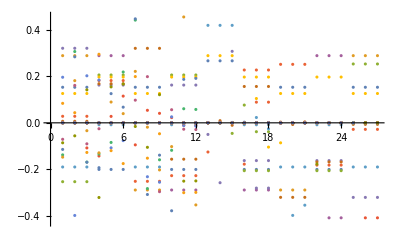

```mathematica
ListPlot[Table[Re[evecs[[i]]],{i,Range[Length[evecs]]}]]
```

```mathematica
ListPlot[Table[Re[evecs[[i]]],{i,Range[Length[evecs]]}]]
```

```mathematica
Manipulate[ListPlot[Re[evecs[[i]]]],{i,Range[Length[evecs]]}]
```

```mathematica
fmode.evecs[[maxIdx]]
```

```mathematica
evecs[[maxIdx]]*.evecs[[maxIdx]]
```

1.+0. ⅈ

```mathematica
fmode.fmode
```

1

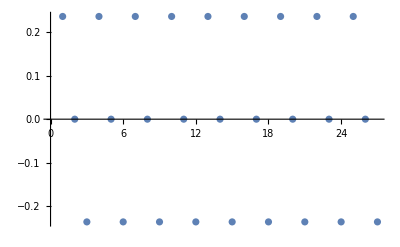

```mathematica
ListPlot[fmode]
```

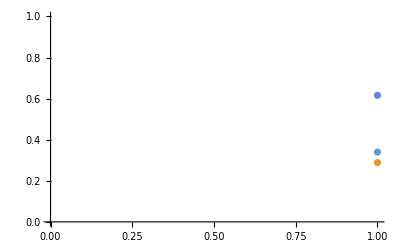

```mathematica
ListPlot[Table[evecs[[i]],{i,Range[Length[evecs]]}]]
```

```mathematica
fmode.Re[evecs[[maxIdx]]]
```

0.947323

```mathematica
γ
```

```mathematica
Log10[1.2201407406990124*^-47/2.232298141701227*^-28]
```

-19.2623

```mathematica
ArrayReshape[soln[[1]],{2,Length[soln[[1]]]} ]
```

{{0.1,6.39915×10^-16,0.15,-2.04381×10^-16,0.2,1.14181×10^-16,0.25,5.29715×10^-17,0.3,8.49045×10^-33,0.35,4.25494×10^-16,0.4,1.36351×10^-16,0.45,-5.57639×10^-16},{0.5,-3.72658×10^-17,0.55,2.17013×10^-16,0.6,1.34746×10^-16,0.65,-5.54172×10^-34,0.7,-3.60054×10^-32,0.75,-3.038×10^-32,0.8,-7.68×10^-16,0.85,-4.72436×10^-33}}

```mathematica
{pts, gamma} = Transpose@soln[[1]];
```

```mathematica
logdata = Transpose@{pts,Log10[Abs[gamma/γ]]}
```

{{0.1,12.4574},{0.15,11.9617},{0.2,11.7088},{0.25,11.3753},{0.3,-4.41982},{0.35,12.2801},{0.4,11.7859},{0.45,12.3976},{0.5,11.2226},{0.55,11.9877},{0.6,11.7808},{0.65,-5.60511},{0.7,-3.79238},{0.75,-3.86616},{0.8,12.5366},{0.85,-4.67441}}

```mathematica
soln[[1]]
```

{{0.1,6.39915×10^-16},{0.15,-2.04381×10^-16},{0.2,1.14181×10^-16},{0.25,5.29715×10^-17},{0.3,8.49045×10^-33},{0.35,4.25494×10^-16},{0.4,1.36351×10^-16},{0.45,-5.57639×10^-16},{0.5,-3.72658×10^-17},{0.55,2.17013×10^-16},{0.6,1.34746×10^-16},{0.65,-5.54172×10^-34},{0.7,-3.60054×10^-32},{0.75,-3.038×10^-32},{0.8,-7.68×10^-16},{0.85,-4.72436×10^-33}}

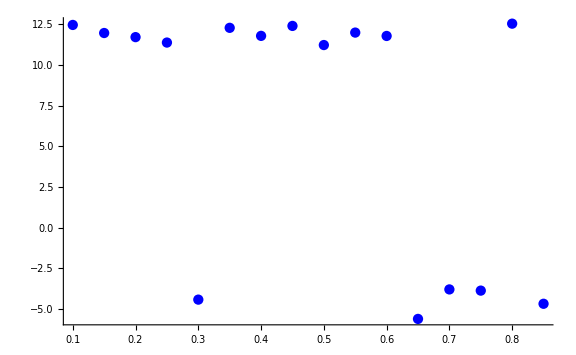

```mathematica
markers = {Graphics[{Blue, Disk[]}],Graphics[{Red,Rectangle[]}],Graphics[{Green, Disk[]}]};
colors = {Blue,Red,Green};
plots = {};
For[lidx=1,lidx<Length[soln]+1,lidx++,
AppendTo[plots,ListPlot[logdata ,PlotLegends->modelist[[lidx,2]],(*PlotMarkers->{markers[[lidx]],0.02}*)Joined->False,PlotStyle->colors[[lidx]]]];
]
Show[plots,PlotRange->All,ImageSize-> Large]
```

```mathematica
Log10[1/31^6]//N
```

-8.94817

```mathematica
Log10[1/3^(2*.9)]
```

-0.858818

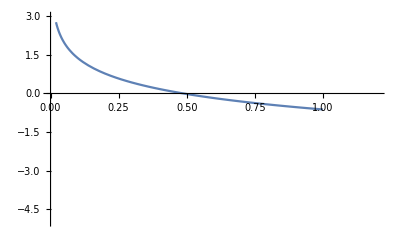

```mathematica
Plot[Log10[3/(4π d^2)],{d,0.02,1},PlotRange->{{0,1.2},{-5,3}}]
```

## radiation in the time domain

```mathematica
(*initialize the state vector. excite central 9 atoms in m=0 states*)

(*state = Array[Subscript[b, ##]&,dim];
excitedIdcs = Flatten@Table[(deg*atomnum-1)/2+deg*√atomnum i+deg j-1,{i,{-1,0,1}},{j,{-1,0,1}}];
state[[excitedIdcs]]=1; *)
```

## tests

pick out element from G depending on the dressing polarization of atoms i,j. Ferromagnetic:

```mathematica
Clear[i]
```

```mathematica
e[k_]:=Subscript[e, 1](*k is the atom number*)
```

```mathematica
e[2]
```

{1,0,0}

Anti-ferromagnetic:

```mathematica
e[k_]:=(-1)^k Subscript[e, 1]
```

In-plane:

```mathematica
e[k_]:=Subscript[e, 2];
```

```mathematica
duh = {x,x^2}
```

{x,x^2}

```mathematica
f[x_]=duh[[2]]
```

```mathematica
g[x_]=duh[[1]]
```

x

```mathematica
g[2]
```

2

made a mistake in my polarization basis. no zeeman splitting, and ferro/anti-ferro states have x polarizations. use spherical basis for atomic states; need to work in Jz basis because this is good quantum number here.

Px excitation is superposition of P_(-1,+1). Likewise for Py.  X=1/(√2)(-1-+1), Y=-ⅈ/(√2)(-1++1). So with the basis {-1,+1,|0⟩}, the x,y,z states are:

```mathematica
1/(√2)(Subscript[esphr, 1]-Subscript[esphr, 2]) (*recover x*)
-ⅈ/(√2)(Subscript[esphr, 1]+Subscript[esphr, 2]) (*recover y*)
{1,0,0}
{0,1,0}
```

Cross product expression for G*p:

```mathematica
Clear[d,λ,k,γ]
i = 10; j = 10;μ=1; ν=2;
u=d λ Subscript[r, i,j];
Gij= e[i]*.GdotP[{rx,ry,rz},e[j] ];
Ωμνij=If[i==j,0,(6 π γ)/k^3 Re[Gij]/.{rx -> u[[1]],ry->u[[2]] ,rz-> u[[3]]}  ];
γμνij=Piecewise[{{γ,i==j&& μ==ν},{(6 π γ)/k^3 Im[Gij]/.{rx -> u[[1]],ry->u[[2]] ,rz-> u[[3]]} ,i≠j},{γ/k^2,i==j}}];
{Ωμνij,γμνij}
(*Hfull[[3i-1+ν,3j-1+μ]]= Subscript[Δ, 2-μ] KroneckerDelta[i,j]KroneckerDelta[μ,ν]+Ωμνij(1-KroneckerDelta[i,j])+ⅈ γμνij;*)
```

{0,γ/k^2}

```mathematica
e[2]
```

{1,0,0}

```mathematica
k =
```

```mathematica
Gij=e[i]*.GdotP[{rx,ry,rz},e[j]];
Gij/.{rx -> u[[1]],ry->u[[2]] ,rz-> u[[3]]}
```

-11194.2-141687. ⅈ

{-11194.2,33843.8,33843.8}

```mathematica
{Ωμνij,γμνij}
```

{{-8.54507×10^-10,2.58346×10^-9,2.58346×10^-9},{-1.08157×10^-8,-2.34692×10^-10,-2.34692×10^-10}}

```mathematica
e[j_]:=Subscript[e, 1]
period = 0.5 λ;
μ=2;ν=2;i=2;j=2;
d=0.7;
k = 2π/λ;
u=d λ Subscript[r, i,j];
(*rhat = unit[Subscript[r, i,j]];*)
v = {nx,ny,nz};
```

```mathematica
ComplexExpand[e[i]*.GdotP[{x,0,0},e[j]]]
```

(2.45273×10^-15 √(x^2) Cos[8.05537×10^6 √(x^2)])/x^4+(1.97576×10^-8 Sin[8.05537×10^6 √(x^2)])/x^2+ⅈ (-(1.97576×10^-8 Cos[8.05537×10^6 √(x^2)])/x^2+(2.45273×10^-15 √(x^2) Sin[8.05537×10^6 √(x^2)])/x^4)

```mathematica
3{x,y,z}/.{x,y,z}-> Subscript[unit, i,j]
```

{3 x,3 y,3 z}

```mathematica
e[i]*.GdotP[nhat[[]],e[j]matelem ]/.nhat[[]] ->  unit[Subscript[r, i,j]]
```

{1.63434×10^-37+3.33652×10^-38 ⅈ,-8.17168×10^-38-1.66826×10^-38 ⅈ,-8.17168×10^-38-1.66826×10^-38 ⅈ}

```mathematica
e[i]*.GdotP[unit[Subscript[r, i,j]],e[j]matelem ]
```

1.63434×10^-37+3.33652×10^-38 ⅈ

```mathematica
unit[Subscript[r, i,j]]
```

{-1,0,0}

```mathematica
e[1].Gij/.nhat-> Subscript[r, 1,2]
```

1.63434×10^-37+3.33652×10^-38 ⅈ

```mathematica
GdotP[{rx,0,0},{px,py,pz}]
```

{0,(ⅇ^(ⅈ k √(rx^2)) (py-py (1/(k^2 rx^2)-ⅈ/(k √(rx^2)))))/(4 π √(rx^2)),(ⅇ^(ⅈ k √(rx^2)) (pz-pz (1/(k^2 rx^2)-ⅈ/(k √(rx^2)))))/(4 π √(rx^2))}

```mathematica
Limit[Im[GdotP[{x,0,0},{1,0,0}]],x->0]
```

{427350.,0,0}

{-27688.9+72713.7 ⅈ,4610.49-6568.79 ⅈ,0.+0. ⅈ}

```mathematica
e[i]*.GdotP[u,e[j]matelem ]
```

0.+0. ⅈ

```mathematica
Limit[e[i]*.GdotP[{x,0,0},e[j]matelem ],x-> 0]
```

0.

```mathematica
Limit[GdotP[{x,0,0},e[j]matelem ],x-> 0]
```

{0.,0.,0.}

Derivative expr. for G

```mathematica
e[k_]:=Subscript[e, 1]
period = 0.5 λ;
μ=1;ν=2;i=2;j=2;
d=0.7;
k = 2π/λ;
u=d λ Subscript[r, i,j];
v= (e[i]*.GTensor.e[j])/.z->0 //ComplexExpand;(*x polarized for now*)
Ωμνij = If[i==j,0,(6 π γ)/k^3 Re[v/.{x-> u[[1]],y-> u[[2]]}]];
γμνij=If[i==j&& μ==ν,γ,(6 π γ)/k^3 Im[v/.{x-> u[[1]],y-> u[[2]]}]];
Subscript[Δ, μ] KroneckerDelta[i,j]KroneckerDelta[μ,ν]+Ωμνij(1-KroneckerDelta[i,j])+ⅈ γμνij;
{Ωμνij,γμνij}
```

Power::infy: Infinite expression 1/0.^(5/2) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^(5/2) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^(3/2) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{0,Indeterminate}

```mathematica
(*Find the basis eigenvalues of interest by diagonalizing the Hamiltonian and then finding the overlap of the resultant e-vecs with the desired basis vectors*)
{evals,evecs} = Eigensystem[Hfull];
```

```mathematica
fmode =Flatten@Array[Subscript[ecart, 1]&,9](*ferromagnetic state: each atom excited with polarization x:*)
(*afmode = Array[KroneckerDelta[,Mod[#,2(2J+1)]]]*)
```

{1/(√2),-1/(√2),0,1/(√2),-1/(√2),0,1/(√2),-1/(√2),0,1/(√2),-1/(√2),0,1/(√2),-1/(√2),0,1/(√2),-1/(√2),0,1/(√2),-1/(√2),0,1/(√2),-1/(√2),0,1/(√2),-1/(√2),0}

```mathematica
afmode =Flatten@Array[(-1)^# Subscript[ecart, 1]&,9]
```

{-1/(√2),1/(√2),0,1/(√2),-1/(√2),0,-1/(√2),1/(√2),0,1/(√2),-1/(√2),0,-1/(√2),1/(√2),0,1/(√2),-1/(√2),0,-1/(√2),1/(√2),0,1/(√2),-1/(√2),0,-1/(√2),1/(√2),0}

```mathematica
ipmode = Flatten@Array[Subscript[ecart, 2]&,9]
```

{-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0}

```mathematica
{evals,evecs} = Eigensystem[Hfull];
overlap = {};(*list with entries {idx, overlap coefficient}*)
For[i = 1,i<Length[evecs]+1,i++,
AppendTo[overlap,{i,Abs[fmode.evecs[[i]]]}]
]
maxIdx=Sort[overlap,#1[[2]]>#2[[2]]&][[1,1]];
linewidth=Log10[Im[evals[[maxIdx]]]/γ];
```

7.33422

```mathematica
period
```

1.05

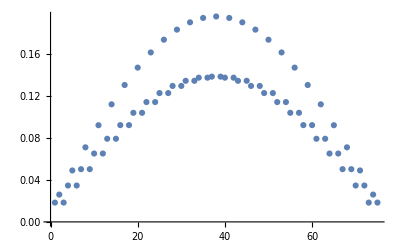

```mathematica
ListPlot[Re[evecs[[maxIdx]]]]
```

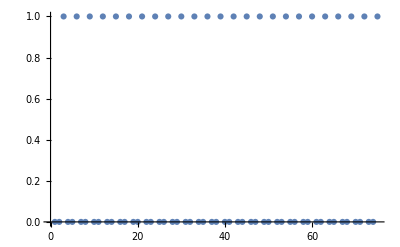

```mathematica
ListPlot[fmode]
```

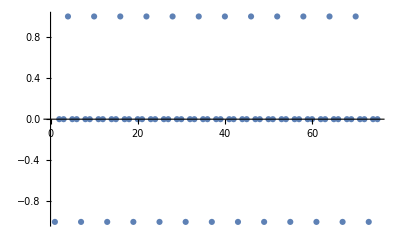

```mathematica
ListPlot[afmode]
```

```mathematica
fmode = Array[KroneckerDelta[2,Mod[#,3]]&,dim];(*anti-ferromagnetic state*)
```

```mathematica
afmode= Array[Boole[(u==1|| u==0)/.u-> Mod[#,6]]&,15]
```

{1,0,0,0,0,1,1,0,0,0,0,1,1,0,0}

```mathematica
Array[Boole[(u==1|| u==0)/.u-> Mod[#,6]]&,12]
```

{1,0,0,0,0,1,1,0,0,0,0,1}

```mathematica
1,2,3,4,5,6,7,8,9,10,11,12,13,14,15
1,0,0,0,0,1,1,0,0,0,0,1,1,0,0
```

every other group of three, use KroneckerDelta[1or2,Mod[#,3]]] to set value to 1.

Build anti/ferromag. states, and then calculate overlap with a given basis vector list

```mathematica
fmode = Array[KroneckerDelta[2,Mod[#,3]]&,9]
```

```mathematica
%
```

{299792458,599584916,899377374,1199169832,1498962290,1798754748,2098547206,2398339664,2698132122}

Check my grid mapping. 2D grid, but only one index to specify atoms

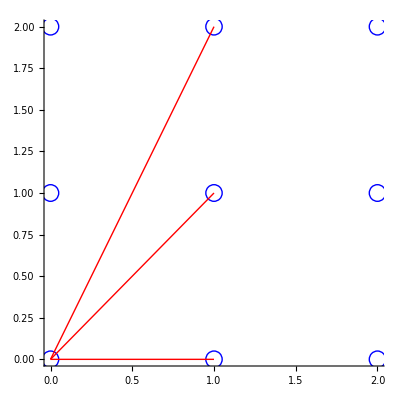

```mathematica
num=√atomnum;
a=1;(*0.7;*)
r[i_,j_] :=Graphics[{Red,Line[{a{Mod[i-1,num], Floor[(i-1)/num]},a{Mod[j-1,num],Floor[(j-1)/num]}}]}];
Show[Table[Graphics[{Blue,Circle[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}],{i,Range[num^2]}],Table[r[1,j],{j,{2,5,8}}],(*PlotLegends-> Placed[{"hi"},{1/(a num)//N,1/(a num)//N}],*) Axes->True,PlotRange->{{0,a (num-1)},{0,(a num-1)}}]
```

What 1D atom idx corresponds to (i,j)?

```mathematica
idx[i_,j_,n_]:=(i-1)n+j//Simplify;
```

```mathematica
idx[2,2,n]
```

2+n

```mathematica
idx[1,1,n]//Simplify
```

(2+n)/2

```mathematica
Solve[{n+2== 2 (α  + β),n==α +β n },{α,β} ]
```

{{α→n^2/(2 (-1+n)),β→-(2-n)/(2 (-1+n))}}

```mathematica
Clear[i,j]
```

```mathematica
{Mod[i-1,num],Floor[(i-1)/num]}/.{i-> 2,j-> 2}
```

{1,0}

```mathematica
1/(a num)//N
```

0.0666667

```mathematica
Legended
```

```mathematica
r[i_,j_] :=a{Mod[j-1,num]-Mod[i-1,num],Floor[(j-1)/num]-Floor[(i-1)/num]};
```

```mathematica
r[1,15]
```

{2.8,1.4}

```mathematica
υ = Table[x^2+y^2,{x,{-1,0,1}},{y,{-1,0,1}}]
```

{{2,1,2},{1,0,1},{2,1,2}}

```mathematica
{1,0,1}.υ
```

{4,2,4}